```mathematica
Задание 1
```

Задание

```mathematica
M1 = RandomInteger[{-10,10},{6,6}];
```

```mathematica
{lu, p, r} = LUDecomposition[M1];
```

```mathematica
u = UpperTriangularize[lu];
l=LowerTriangularize[lu, -1] +IdentityMatrix[6] ;
```

```mathematica
P=IdentityMatrix[6];
```

```mathematica
p
```

{6,4,1,5,3,2}

```mathematica
PP = (P[[#]]&)/@p;
```

```mathematica
PP.M1 == l.u
```

True

```mathematica
{qq,qr} = QRDecomposition[M1];
```

```mathematica
M1==Transpose[qq].qr
```

True

```mathematica
Задание 2
```

```mathematica
M2 = RandomReal[{-10,10},{6,6}];
```

```mathematica
{lu2, p2, r2} = LUDecomposition[M2];
```

```mathematica
u2 = UpperTriangularize[lu2];
l2=LowerTriangularize[lu2, -1] +IdentityMatrix[6] ;
```

```mathematica
P2=IdentityMatrix[6];
```

```mathematica
p2
```

{6,5,4,1,2,3}

```mathematica
PP2 = (P2[[#]]&)/@p2;
```

```mathematica
PP2.M2 == l2.u2
```

True

```mathematica
r2
```

13.3801

```mathematica
Norm[PP2.M2 - l2.u2, Infinity]
```

5.32907×10^-15

```mathematica
{qq2,qr2} = QRDecomposition[M2];
```

```mathematica
M2==Transpose[qq2].qr2
```

True

```mathematica
Задание 3.
```

```mathematica
MS=RandomReal[{0,10},{5,5}];
MS=MS+ Transpose[MS];
HermitianMatrixQ[MS]
```

True

```mathematica
qrF[AA_]:=Module[{A=AA, Q,R, n=0, ers},
ers={Norm[Eigenvalues[AA] -Diagonal[A]]};
While[Norm[Eigenvalues[A] - Diagonal[A]]> 10^-2,
ers=Append[ers,Norm[Eigenvalues[AA] -Diagonal[A]]];
{Q,R}= QRDecomposition[A];
A= R.Transpose[Q];
++n];
{n,ers}];
```

```mathematica
{Nsteps, errors}=qrF[MS];
Nsteps
```

413

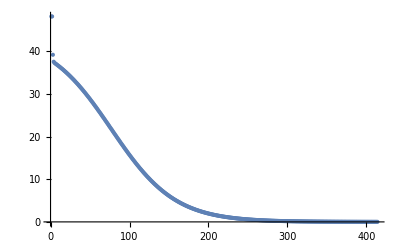

```mathematica
ListPlot[errors]
```

```mathematica
Задание 4.
```

```mathematica
n=10;
```

```mathematica
mSm =SparseArray[{i_,j_}/;(i+j==n):> 1, {n,n}];
```

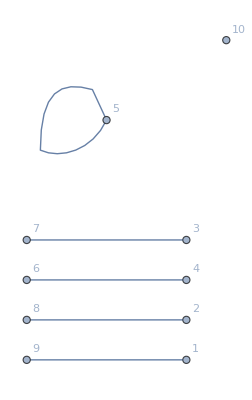

```mathematica
g =AdjacencyGraph[Normal[mSm], VertexLabels->Automatic]
```

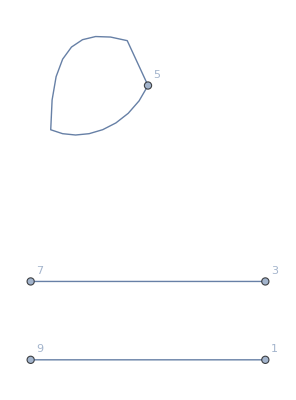

```mathematica
gr =VertexDelete[g, Table[i,{i,2,10,2}]]
```

```mathematica
IncidenceMatrix[gr] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 2
0 | 1 | 0
1 | 0 | 0)

```mathematica
AdjacencyMatrix[gr] // MatrixForm
```

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)